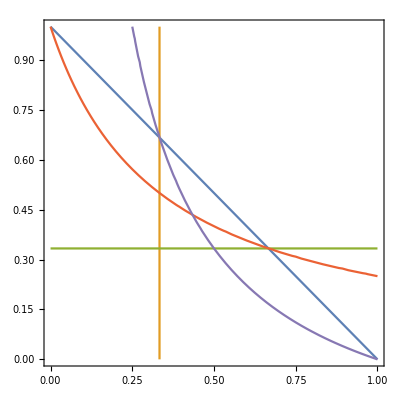

```mathematica
ch = 1.5; 
cm = 0.5;
ContourPlot[{q1 + q2==1,q1==cm/ch,q2==cm/ch,q1==(cm/ch)*(1-q2)/q2,q2==(cm/ch)*(1-q1)/q1}, {q1, 0,1}, {q2, 0,1}]
```

```mathematica
Solve[ch + cm/q1==cm/(q1*q2),q1]
```

{{q1→(cm-cm q2)/(ch q2)}}

```mathematica
possible[q1_,q2_]:= {2*ch, ch + cm/q1, ch + cm/q2,  cm/(q1*q2), cm/q1 + cm/q2}
```

```mathematica
sequences = {1->"(1)(2)", 2->"<1>(2)", 3->"(1)<2>", 4->"<1|2>", 5->"<1><2>"};
```

```mathematica
Min[possible[1/2,1/2]]
```

```mathematica
cost[q1_,q2_]:=Min[possible[q1,q2]]
```

```mathematica
points = Flatten[Table[Table[{i, j}, {i, .01, 1-0.01, 0.1}], {j, 0.01, 1 - 0.01, 0.1}],1];
```

```mathematica
grouped = GatherBy[Map[{Config[#[[1]], #[[2]]],#}&, points],First];
```

```mathematica
Summarize[x_]:={Mean[Map[First[#]&,x]],Mean[Map[Last[#]&,x]]}
```

```mathematica
points = Map[Summarize,grouped]
```

{{1,{0.16,0.16}},{2,{0.641818,0.146364}},{4,{0.669459,0.669459}},{3,{0.146364,0.641818}},{5,{0.443333,0.443333}}}

```mathematica
labels=Style[Text[#[[1]]/.sequences,#[[2]]], Background->White]&/@points;
```

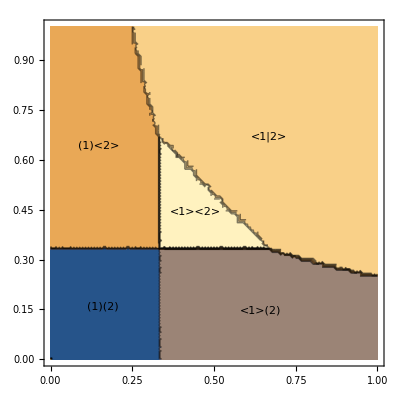

```mathematica
ContourPlot[Config[q1,q2],{q1,0,1},{q2,0,1},Epilog->labels]
```

```mathematica
Plot3D[cost[q1,q2],{q1,0,1},{q2,0,1},Epilog->labels]
```

-Graphics3D-

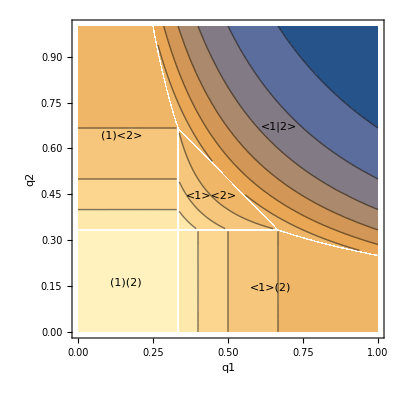

```mathematica
g=ContourPlot[cost[q1,q2],{q1,0,1},{q2,0,1},Epilog->labels,AxesLabel->{"q1","q2"}]
```

```mathematica
Export["diagram.pdf", g]
```

diagram.pdf